New in CIP 1.1

QSPR with small Data Set

This tutorial demonstrates new functions of CIP version 1.1 that complement the discussion in textbook

Achim Zielesny, From Curve Fitting to Machine Learning: An illustrative Guide to scientific Data Analysis and Computational Intelligence, Berlin 2011. (Springer: Intelligent Systems Reference Library, Volume 18).

CIP is available at http://www.gnwi.de.

```mathematica
Clear["Global`*"];
<<CIP`Utility`
<<CIP`ExperimentalData`
<<CIP`DataTransformation`
<<CIP`Graphics`
<<CIP`MLR`
<<CIP`Perceptron`
```

A Quantitative Structure-Property Relationship (QSPR) is a model that maps features of chemical structures or reactions (the input) to a quantity of interest (the output). The features of a chemical structure or reaction are so called (structural/molecular) descriptors, i.e. characteristic numbers which are calculated for the specific structure/reaction. The output quantity of interest is usually measured experimentally. QSPR models may be constructed with machine learning approaches.

The following QSPR data set comprises 183 input/output (I/O) pairs that each represent a single chemical compound. Each input vector consists of 155 components where each component is a structural descriptor. Each corresponding output vector contains a single experimentally measured value for a compound-related physico-chemical quantity.

```mathematica
dataSet=CIP`ExperimentalData`GetQSPRDataSet01[];
CIP`Graphics`ShowDataSetInfo[{"IoPairs","InputComponents","OutputComponents"},dataSet]
```

Number of IO pairs = 183

Number of input components = 155

Number of output components = 1

At first glance the usefulness of the whole data set is in doubt since the number of input components is nearly equal to the number of I/O pairs, i.e. a linear method (MLR - Multiple Linear Regression) is likely to be able to establish a perfect relationship between the molecular descriptors and the corresponding physico-chemical quantity

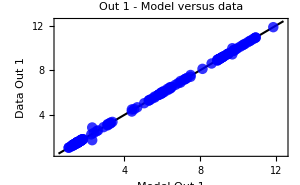

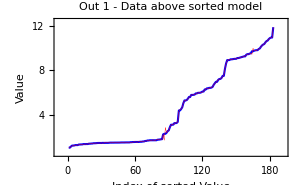

Definition of 'Residual (absolute)': Data - Model

Out 1 : Residual (absolute): Mean/Median/Maximum Value = 2.44×10^-2 / 1.83×10^-6 / 5.7×10^-1

Root mean squared error (RMSE) = 7.145×10^-2

Out 1 : Correlation coefficient = 0.99978

```mathematica
mlrInfo=CIP`MLR`FitMlr[dataSet];
pointSize=0.025;
CIP`MLR`ShowMlrSingleRegression[{"ModelVsDataPlot","SortedModelVsDataPlot","AbsoluteResidualsStatistics","RMSE","CorrelationCoefficient"},dataSet,mlrInfo,GraphicsOptionPointSize->pointSize];
```

but without any predictive power: The model is a pure data representation (look-up table). This may be shown by a partitioning of the whole data into a training and a test set of equal size with a number of heuristic optimization trials of both sets (see tutorial QSPR with MLR for details):

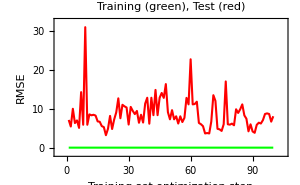

```mathematica
trainingFraction=0.5;
numberOfTrainingSetOptimizationSteps=100;
blackListLength=50;
mlrTrainOptimization=CIP`MLR`GetMlrTrainOptimization[dataSet,trainingFraction,numberOfTrainingSetOptimizationSteps,UtilityOptionBlackListLength->blackListLength];
CIP`MLR`ShowMlrTrainOptimization[mlrTrainOptimization];
```

```mathematica
bestOptimization="MinimumDeviation";
bestRegressionStep=CIP`MLR`GetBestMlrRegressOptimization[mlrTrainOptimization,UtilityOptionsBestOptimization->bestOptimization]
```

19

Training Set:

Root mean squared error (RMSE) = 1.618×10^-2

Definition of 'Residual (absolute)': Data - Model

Out 1 : Residual (absolute): Mean/Median/Maximum Value = 5.31×10^-3 / 3.73×10^-14 / 8.×10^-2

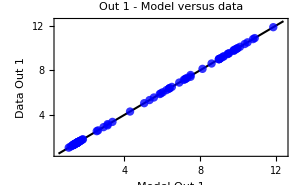

Out 1 : Correlation coefficient = 0.99999

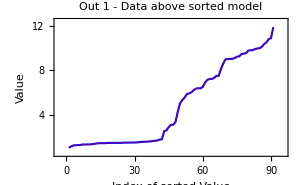

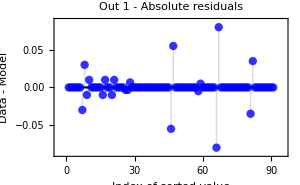

Test Set:

Root mean squared error (RMSE) = 3.203

Definition of 'Residual (absolute)': Data - Model

Out 1 : Residual (absolute): Mean/Median/Maximum Value = 1.48 / 5.94×10^-1 / 1.71×10^1

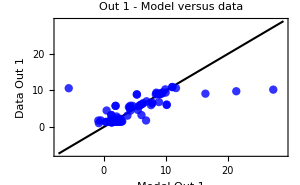

Out 1 : Correlation coefficient = 0.735226

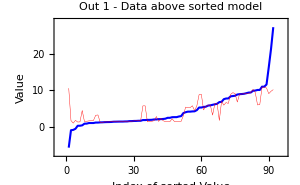

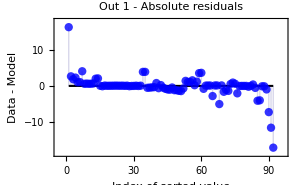

```mathematica
trainingAndTestSetList=mlrTrainOptimization[[3]];
mlrInfoList=mlrTrainOptimization[[4]];
trainingAndTestSet=trainingAndTestSetList[[bestRegressionStep]];
bestMlrInfo=mlrInfoList[[bestRegressionStep]];
pointSize=0.02;
CIP`MLR`ShowMlrRegressionResult[{"RMSE","AbsoluteResidualsStatistics","ModelVsDataPlot","CorrelationCoefficient","SortedModelVsDataPlot","AbsoluteSortedResidualsPlot"},trainingAndTestSet,bestMlrInfo,GraphicsOptionPointSize->pointSize]
```

Whereas the training data are nearly perfectly described the prediction of the test data is poor and not convincing. Thus the size of the input space has to be reduced to the most relevant input components for I/O mapping in order to proceed. If the relevance of input components is successively evaluated with MLR (see tutorial Minimal Model for the WDBC Data for details)

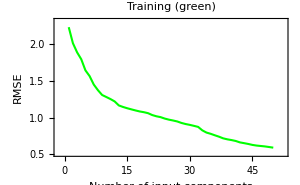

Input component list = {43,102,111,128,67,100,116,97,72,14,86,66,6,127,77,17,98,7,38,63,13,120,8,71,85,135,42,146,107,11,53,33,39,25,76,88,141,151,61,62,136,68,119,80,74,79,46,27,129,28}

```mathematica
trainingAndTestSet={dataSet,{}};
numberOfInclusionsPerStepList=Table[1,{50}];
mlrInputComponentRelevanceListForRegression=CIP`MLR`GetMlrInputInclusionRegress[trainingAndTestSet,UtilityOptionsInclusionsPerStep->numberOfInclusionsPerStepList];
CIP`MLR`ShowMlrInputRelevanceRegress[mlrInputComponentRelevanceListForRegression]
```

an arbitrary choice of the 10 detected most relevant input components may be taken.

```mathematica
inputComponentInclusionList={43,102,111,128,67,100,116,97,72,14};
reducedDataSet=CIP`DataTransformation`IncludeInputComponentsOfDataSet[dataSet,inputComponentInclusionList];
```

The above partitioning in equally sized training and test data sets

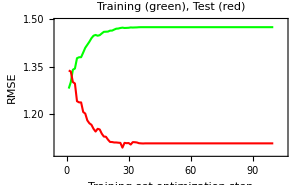

```mathematica
trainingFraction=0.5;
numberOfTrainingSetOptimizationSteps=100;
blackListLength=50;
mlrTrainOptimization=CIP`MLR`GetMlrTrainOptimization[reducedDataSet,trainingFraction,numberOfTrainingSetOptimizationSteps,UtilityOptionBlackListLength->blackListLength];
CIP`MLR`ShowMlrTrainOptimization[mlrTrainOptimization];
```

```mathematica
bestOptimization="MinimumDeviation";
bestRegressionStep=CIP`MLR`GetBestMlrRegressOptimization[mlrTrainOptimization,UtilityOptionsBestOptimization->bestOptimization]
```

2

Training Set:

Root mean squared error (RMSE) = 1.301

Definition of 'Residual (absolute)': Data - Model

Out 1 : Residual (absolute): Mean/Median/Maximum Value = 9.9×10^-1 / 7.62×10^-1 / 4.

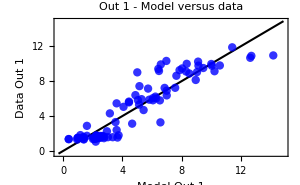

Out 1 : Correlation coefficient = 0.925772

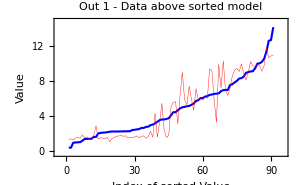

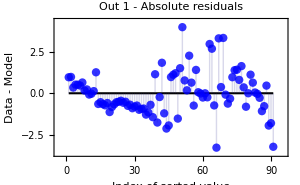

Test Set:

Root mean squared error (RMSE) = 1.335

Out 1 : Root mean squared error (RMSE) = 1.335

Definition of 'Residual (absolute)': Data - Model

Out 1 : Residual (absolute): Mean/Median/Maximum Value = 1.04 / 8.67×10^-1 / 3.61

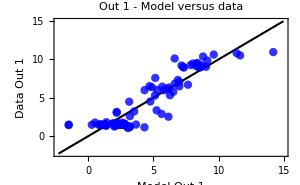

Out 1 : Correlation coefficient = 0.917111

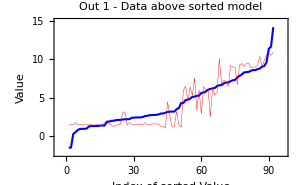

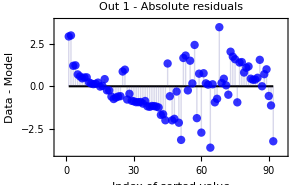

```mathematica
trainingAndTestSetList=mlrTrainOptimization[[3]];
mlrInfoList=mlrTrainOptimization[[4]];
trainingAndTestSet=trainingAndTestSetList[[bestRegressionStep]];
bestMlrInfo=mlrInfoList[[bestRegressionStep]];
pointSize=0.02;
CIP`MLR`ShowMlrRegressionResult[{"RMSE","AbsoluteResidualsStatistics","ModelVsDataPlot","CorrelationCoefficient","SortedModelVsDataPlot","AbsoluteSortedResidualsPlot"},trainingAndTestSet,bestMlrInfo,GraphicsOptionPointSize->pointSize]
```

now leads to an at least semi-quantitative model with similar predictivity for training and test data. The use of a non-linear machine learning method like a perceptron-type neural network with 3 hidden neurons

```mathematica
numberOfHiddenNeurons=3;
```

may allow a further (arbitrary) reduction of the input component space:

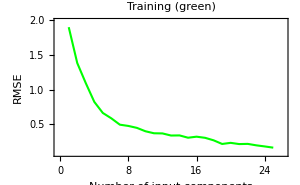

Input component list = {43,32,34,22,90,147,1,109,113,118,26,85,14,41,80,105,9,154,133,28,58,89,23,152,94}

```mathematica
trainingAndTestSet={dataSet,{}};
numberOfInclusionsPerStepList=Table[1,{25}];
perceptronInputComponentRelevanceListForRegression=CIP`Perceptron`GetPerceptronInputInclusionRegress[trainingAndTestSet,numberOfHiddenNeurons,UtilityOptionsInclusionsPerStep->numberOfInclusionsPerStepList];
CIP`Perceptron`ShowPerceptronInputRelevanceRegress[perceptronInputComponentRelevanceListForRegression]
```

If the 5 most relevant detected input components are used

```mathematica
inputComponentInclusionList={43,32,34,22,90};
reducedDataSet=CIP`DataTransformation`IncludeInputComponentsOfDataSet[dataSet,inputComponentInclusionList];
```

with equally sized and optimized training and test sets

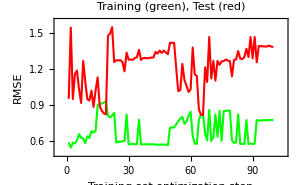

```mathematica
trainingFraction=0.5;
numberOfTrainingSetOptimizationSteps=100;
blackListLength=50;
perceptronTrainOptimization=CIP`Perceptron`GetPerceptronTrainOptimization[reducedDataSet,numberOfHiddenNeurons,trainingFraction,numberOfTrainingSetOptimizationSteps,UtilityOptionBlackListLength->blackListLength];
CIP`Perceptron`ShowPerceptronTrainOptimization[perceptronTrainOptimization];
```

```mathematica
bestOptimization="MinimumDeviation";
bestRegressionStep=CIP`Perceptron`GetBestPerceptronRegressOptimization[perceptronTrainOptimization,UtilityOptionsBestOptimization->bestOptimization]
```

65

Training Set:

Root mean squared error (RMSE) = 8.267×10^-1

Definition of 'Residual (absolute)': Data - Model

Out 1 : Residual (absolute): Mean/Median/Maximum Value = 5.88×10^-1 / 3.61×10^-1 / 2.32

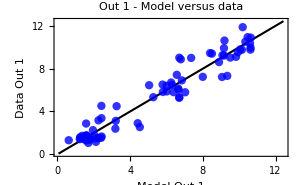

Out 1 : Correlation coefficient = 0.970638

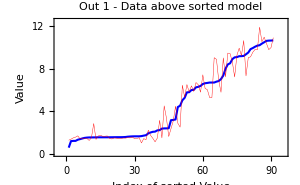

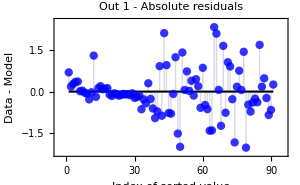

Test Set:

Root mean squared error (RMSE) = 8.223×10^-1

Definition of 'Residual (absolute)': Data - Model

Out 1 : Residual (absolute): Mean/Median/Maximum Value = 5.21×10^-1 / 3.51×10^-1 / 4.93

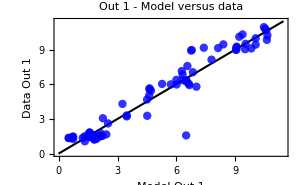

Out 1 : Correlation coefficient = 0.969942

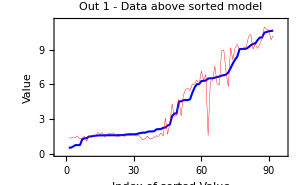

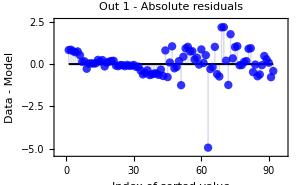

```mathematica
trainingAndTestSetList=perceptronTrainOptimization[[3]];
perceptronInfoList=perceptronTrainOptimization[[4]];
trainingAndTestSet=trainingAndTestSetList[[bestRegressionStep]];
bestPerceptronInfo=perceptronInfoList[[bestRegressionStep]];
pointSize=0.02;
CIP`Perceptron`ShowPerceptronRegressionResult[{"RMSE","AbsoluteResidualsStatistics","ModelVsDataPlot","CorrelationCoefficient","SortedModelVsDataPlot","AbsoluteSortedResidualsPlot"},trainingAndTestSet,bestPerceptronInfo,GraphicsOptionPointSize->pointSize]
```

an improvement in predictivity on both sets is achieved with half the number of input components compared to the linear MLR approach.